```mathematica
SetDirectory["~/jennaproject/data"]
```

/Users/Jenna/jennaproject/data

```mathematica
filelist=Import["~/jennaproject/data/alpha_files.txt","List"]
```

{alpha_b2_0.0_br_0.001.txt,alpha_b2_0.0_br_0.002.txt,alpha_b2_0.0_br_0.003.txt,alpha_b2_0.0_br_0.004.txt,alpha_b2_0.0_br_0.005.txt,alpha_b2_0.0_br_0.006.txt,alpha_b2_0.0_br_0.007.txt,alpha_b2_0.0_br_0.008.txt,alpha_b2_0.0_br_0.009.txt,alpha_b2_0.0_br_0.010.txt,alpha_b2_0.0_br_0.011.txt,alpha_b2_0.0_br_0.012.txt,alpha_b2_0.0_br_0.013.txt,alpha_b2_0.0_br_0.014.txt,alpha_b2_0.0_br_0.015.txt,alpha_b2_0.0_br_0.016.txt,alpha_b2_0.0_br_0.017.txt,alpha_b2_0.0_br_0.018.txt,alpha_b2_0.0_br_0.019.txt,alpha_b2_0.0_br_0.020.txt}

```mathematica
Dimensions[filelist]
```

{20}

```mathematica
bfiles=Import[filelist[[#]],"Table"]&/@Range[1,Dimensions[filelist][[1]]];
```

```mathematica
bfile0=Import["~/jennaproject/data/alpha_b2_0.0_br_0.000.txt","Table"]
```

{{1.01397,40.3585,0.987729},{1.02546,38.4521,1.08986},{1.02469,35.1383,0.694417},{1.02113,59.6557,1.00057},{1.02231,43.6802,0.7664},{1.00138,38.7481,1.05607},{1.02209,31.6935,1.11739},{0.987045,53.9498,0.941586},{0.994499,41.8784,0.756433},{0.990305,46.4495,0.589183},{0.989133,48.9834,1.09354}}

```mathematica
Mean[bfile0[[All,1]]]
```

1.00836

```mathematica
Dimensions[bfiles]
```

{20,11,3}

```mathematica
bpts=Mean[bfiles[[#,All,1]]]&/@Range[1,Dimensions[bfiles][[1]]]
```

{1.0082,1.00803,1.00787,1.00771,1.00755,1.0074,1.00725,1.0071,1.00696,1.00682,1.00669,1.00655,1.00642,1.0063,1.00618,1.00606,1.00594,1.00583,1.00571,1.00561}

```mathematica
bvals=Range[0.001,0.02,0.001]
```

{0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02}

```mathematica
Dimensions[bvals]
```

{20}

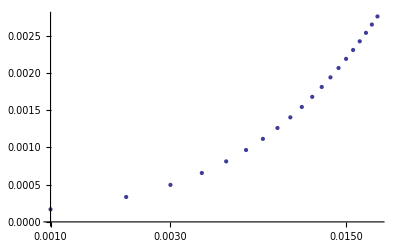

```mathematica
ListLogLinearPlot[{bvals,-bpts+Mean[bfile0[[All,1]]]}ᵀ]
```